The full algorithm to find a path to have the algorithm working.

### Testing RegionMember function on polygon

```mathematica
Manipulate[With[{f=BSplineFunction[{{0.5,0.05},{1.05,0.7},{0.4,1.5},{-1.15,0.85},{-0.75,0.02},{-0.93,-1},{0.2,-1.3},{1.05,-0.83}},SplineClosed->True]},reg2=Polygon[Table[f[t],{t,0,.99,0.01}]];
rm=RegionMember[reg2];];
Column[{Graphics[{Point[p],EdgeForm[{Red,Thick}],Yellow,reg2},PlotRange->Table[{-2,2},{2}](*,Point[RegionNearest[reg,p]],Blue*)],Row[{"Region Member: ",rm[p]}]}],{{p,{0.5,0.5}},Locator}]
```

### Testing Nearest Region function on polygon

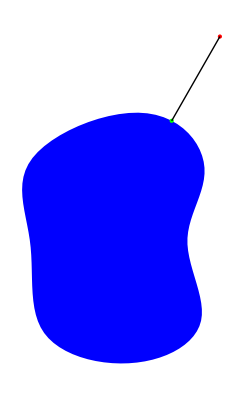

```mathematica
p={1,2};
pn=RegionNearest[reg,p];
Graphics[{Blue,reg2,Red,PointSize[Large],Point[p],Green,Point[pn],Black,Line[{pn,p}]}]
```

### Plotting the actual region (parametric form!)

```mathematica
makeRegionList[ψa_ , ps1_, ps2_]:= Module[{pra,γa,cola, regionlist},

(*ψa is  angle to the collision point *)
cola = 1/2{Cos[ ψa ],Sin[ψa ]}; (*collision point*)
pra= 2 Abs[ps1.cola-ps2.cola]; (*perpendicular distance*)
γa= ArcCos[1-2pra];(*reachable angle for other robot after first robot collides*)

regionlist = Polygon[Table[-cola+1/2{Cos[a],Sin[a]},{a,  ψa - γa ,ψa +γa,γa/20}]];
Return[regionlist]
]

ifInChord[c_, ψa_, p_, γa_, r_]  := (
(*first test if inside the circle centered at c with radius r*)
If[(p⟦1⟧-c⟦1⟧)^2 + (p⟦2⟧-c⟦2⟧)^2> r^2, Return [False]]; 
(*second test if in the half-plane defined by the chord from ψa-γa to ψa+γa, inclusive*)
 (c⟦1⟧-p⟦1⟧) Cos[ψa]+(c⟦2⟧-p⟦2⟧) Sin[ψa]≤ -1/2Cos[γa]
)

ifInRegion[s1_,s2_, nearest_, ψa_] := Module[{θ , α,  γa, d, c ,r= 1/2, cola, pra,ps1,ps2},
{ps1,ps2} = {s1,s2};
d = Norm[ps1-ps2];(*distance between robots*)
θ = ArcTan[ps1⟦1⟧-ps2⟦1⟧,ps1⟦2⟧-ps2⟦2⟧]; (*angle between the two particles with respect to x-axis. This rotates the Δ-Config space*)
α = 2 ArcSin[d]; (*angular arc unreachable by robots in one move (there are two of these). Reachable set for first collision is 2π-2α.*)
c= 1/2{Cos[ψa-π], Sin[ψa-π]}; (*Center of the circle that the chord is a part of*)
cola = 1/2{Cos[ψa ],Sin[ψa ]};(*collision point for robot 2 -- where it hits the circular boundary*)
pra= 2 Abs[ps1.cola-ps2.cola]; (*perpendicular distance: maximum height of chord to boundary *)
γa= ArcCos[1-2pra];(*reachable angle for other robot after first robot collides*)
If[ifInChord[c, ψa, Flatten@nearest, γa, r], Return[True] ,Return[False]];
]
findHit[ps1_,ps2_, nearest_] := Module[(*This function finds the psi of the chord when it has two points of it*)
{  Δs (*beginning delta of the robots*)
, η (*The angle of the chord *)},
Δs = ps2 - ps1;
η = ArcTan[Δs⟦1⟧ - nearest⟦1⟧ , Δs⟦2⟧ - nearest⟦2⟧];

If[Cos[η]≥  0 ,Return [η- π/2] , Return [η+ π/2]]
]
findPsi[s1_,s2_,nearest_] := Module[{ψ,d, θ,α,ps1,ps2},
{ps1,ps2} = {s1,s2};
d = Norm[ps1-ps2];(*distance between robots*)
θ = ArcTan[ps1⟦1⟧-ps2⟦1⟧,ps1⟦2⟧-ps2⟦2⟧]; (*angle between the two particles*)
α = 2 ArcSin[d]; (*anglular arc unreachable by robots*)
If[ifInRegion[ps1,ps2, Flatten@nearest, θ+α/2-π/2],ψ= θ+α/2-π/2,
If[ifInRegion[ps1,ps2, Flatten@nearest,  θ-α/2+π/2],  ψ= θ-α/2+π/2,
ψ= findHit[ps1,ps2, Flatten@nearest];
If[ifInRegion[ps1,ps2, Flatten@nearest,ψ]≠ True,
ψ= ψ+ π]
]];

Return[ψ]
]

makeReachableSet[s1_, s2_] := Module[{d, θ, α,ψa ,pra,γa,cola, γa2, polyline1, polyline2, polyline3, polyline4, finalpoly, reg,ps1,ps2},
{ps1,ps2}= {s1,s2};
d = Norm[ps1-ps2];(*distance between robots*)

θ = ArcTan[ps1⟦1⟧-ps2⟦1⟧,ps1⟦2⟧-ps2⟦2⟧]; (*angle between the two particles*)
α = 2 ArcSin[d]; (*anglular arc unreachable by robots*)
cola = 1/2{Cos[ψa ],Sin[ψa ]}; (*collision point*)
pra= 2 Abs[ps1.cola-ps2.cola]; (*perpendicular distance*)
γa= ArcCos[1-2pra];(*reachable angle for other robot after first robot collides*)
(*THIS IS HORRIBLY COMPLICATED.  SURELY IT SIMPLIFIES.  PLEASE SIMPLIFY IT*)
γa2= ArcCos[1-2pra]/.{ψa-> θ+α/2+π/2};
polyline1 = Table[ 1/2{Cos[θ+α/2+π/2 ],Sin[θ+α/2+π/2 ]}-1/2{Cos[a2+θ+α/2+π/2],Sin[a2+θ+α/2+π/2]},{a2,0,+γa2,γa2/5}]; 
γa2= ArcCos[1-2pra]/.{ψa-> θ-α/2+3π/2};
polyline2 = Table[ 1/2{Cos[θ-α/2+3π/2 ],Sin[θ-α/2+3π/2 ]}-1/2{Cos[a2+θ-α/2+3π/2],Sin[a2+θ-α/2+3π/2]},{a2,-γa2,0,γa2/5}]; 
polyline3= Table[  1/2{Cos[ψa ],Sin[ψa ]}-1/2{Cos[ψa -γa],Sin[ψa -γa]},{ψa,θ+α/2+π/2,θ-α/2+3/2π,(π-α)/20}]; 
polyline4 = Table[  1/2{Cos[ψa ],Sin[ψa ]}-1/2{Cos[ψa +γa],Sin[ψa +γa]},{ψa,θ+α/2+π/2,θ-α/2+3/2π,(π-α)/20}]; 

finalpoly = Join[polyline2,polyline1, polyline4, polyline3];
finalpoly= DeleteDuplicates[Round[finalpoly,1/100000]];
reg = Polygon[finalpoly];

Return[reg]
]
stepToGoal[s1_,s2_,pe1_,pe2_, moves_, pm1_,pm2_]:=Module[{reg, nearest, Δg, ψ, r1, r2, Δr, path, path1, path2, ps1,ps2
},
{ps1,ps2}={s1,s2};
Δg = pe2-pe1;
path = moves;
path1 = pm1;
path2= pm2;
reg = makeReachableSet[ps1,ps2];

nearest = RegionNearest[reg,Flatten@Δg];
Print[nearest];
ψ= findPsi[ps1,ps2,Flatten@nearest];

Δr = 1/2{Cos[ψ],Sin[ψ]};

AppendTo[path, Δr];
r1 = ps1+ Δr;
AppendTo[path1, r1];
r2 = ps2 + Δr;
AppendTo[path2, r2];
Return[{path, path1, path2, r1, r2}]
]
pathToGoal[ps1_,ps2_,pe1_,pe2_]:=Module[{moves, pm1, pm2, r1, r2},
r1 = ps1;
r2 = ps2;

{moves, pm1, pm2, r1, r2}= stepToGoal[r1, r2, pe1, pe2, {{0,0}}, {{0,0}}, {{0,0}}];

While[pe2-pe1 + 0.001< r2-r1&& pe2-pe1-0.001> r2-r1 ,
{moves, pm1, pm2, r1, r2}= stepToGoal[r1, r2, pe1, pe2, moves,pm1, pm2];
];
Return[{moves, pm1, pm2}]
]
```

```mathematica
clipCircle[p_,ϵ_]:=If[Norm[p]>1/2-ϵ,(1/2-ϵ)p/Norm[p],p]; (*keeps robots inside of circle of radius 1/2-ϵ*)
ϵ = 1/1000;
reg;
nearest;
Manipulate[Module[{thickness = 0.005,
d (*distance between robots*),
θ(*angle between the two particles*),
α(*anglular arc unreachable by robots*),
r = 1/40 (*radius of start and end markers*),
(*left robot*) ps1,pe1,
(*right robot*) ps2,pe2,
(*collision point*)pcol1,
pm1, pm2,mvNum,
mvFrac,
path, path1, path2,
Δg ,
c1=Blue,c2 =Magenta},
s1=clipCircle[s1,ϵ];
e1=clipCircle[e1,ϵ];
s2=clipCircle[s2,ϵ];
e2=clipCircle[e2,ϵ];
Δg = {pe2-pe1};




{ps1 ,pe1,ps2,pe2} = {s1,e1,s2,e2};

d = Norm[ps1-ps2];(*distance between robots*)
θ = ArcTan[ps1⟦1⟧-ps2⟦1⟧,ps1⟦2⟧-ps2⟦2⟧]; (*angle between the two particles*)
α = 2 ArcSin[d]; (*anglular arc unreachable by robots*)



{path,path1,path2} = pathToGoal[ps1,ps2,pe1,pe2];


mvNum = Floor[progress*(Length[path]-1)] ;
mvFrac = FractionalPart[progress*(Length[path]-1)];
pm2= If[mvFrac>0,path2⟦mvNum+1,;;⟧+mvFrac*(path2⟦mvNum+2,;;⟧-path2⟦mvNum+1,;;⟧),path2⟦mvNum+1,;;⟧];
pm1 = If[mvFrac>0,path1⟦mvNum+1,;;⟧+mvFrac*(path1⟦mvNum+2,;;⟧-path1⟦mvNum+1,;;⟧),path1⟦mvNum+1,;;⟧];
Graphics[{
(*workspace*)
{Darker[Red], Disk[{0,0},1.025/2]},
{Lighter[Gray,0.8], Disk[{0,0},1/2]},
{White, Disk[{0,0},1/2-ϵ]},
{Lighter[Gray,0.8], Disk[ps2,ϵ]},
PointSize[0.01],
Arrowheads[.03],
{(*wall collision points*)Thickness[3 thickness],c2,Circle[{0,0},1/2,{θ+α/2+π/2,θ-α/2-π/2+2π}]},
{(*wall collision points*)Thickness[3 thickness],c1,Circle[{0,0},1/2,{θ-α/2+π/2,θ+α/2-π/2}]},

{c1,
Table[Arrow[{path1⟦i,;;⟧,path1⟦i+1,;;⟧}],{i,1,mvNum}],
 Arrow[{path1⟦mvNum+1,;;⟧,pm1}],
{If[pm1⟦1⟧==0||pm1⟦2⟧==0||pm1⟦1⟧==1||pm1⟦2⟧==1,{Point@pm1 ,PointSize[0.005],White,Point@pm1 },Point@pm1] }
},


(*plot path of particle 2*)
 {c2,
Table[Arrow[{path2⟦i,;;⟧,path2⟦i+1,;;⟧}],{i,1,mvNum}],
 Arrow[{path2⟦mvNum+1,;;⟧,pm2}],
{If[pm2⟦1⟧==0||pm2⟦2⟧==0||pm2⟦1⟧==1||pm2⟦2⟧==1,{Point@pm2 ,PointSize[0.005],White,Point@pm2 },Point@pm2]}
},
 {(*reachable regions when robot 2 hits first: try many collision points*)
Module[{ψa ,pra,γa,cola},
Table[
ψa=θ+α/2+π/2+c (π-α)/20;
cola = 1/2{Cos[ψa ],Sin[ψa ]};(*collision point for robot 2 -- where it hits the circular boundary*)
pra= 2 Abs[ps1.cola-ps2.cola]; (*perpendicular distance: maximum height of chord to boundary *)
γa= ArcCos[1-2pra];(*reachable angle for other robot after first robot collides*)
{Hue[ψa/(2π)],Point[cola],
{(*draw the chord of reachable locations by robot 1 after robot 2 hits cola*)
Opacity[0.05],Polygon[Table[1/2{Cos[a],Sin[a]},{a,ψa -γa ,ψa +γa,γa/20  (*approximate a chord of a circle by taking many points*)}]]},
(*Line[{1/2{Cos[ψa -γa],Sin[ψa-γa]},1/2{Cos[ψa +γa],Sin[ψa+γa]}}]*)},
{c,0,hits }]]
},
 {(*reachable regions when robot 1 hits first*)
Module[{ψa ,pra,γa,cola, ψ},

Table[
ψa=θ+α/2-π/2+c(π-α)/20;
cola = 1/2{Cos[ψa ],Sin[ψa ]};
pra=  2 Abs[ps1.cola-ps2.cola];(*Abs[(ps1-ps2).{Cos[ψa ],Sin[ψa ]}];*) (*perpendicular distance is the dot product of the two points to cola line (projection)*)
γa= ArcCos[1-2pra];
{Hue[ψa/(2π)],Point[cola],
{Opacity[0.05],EdgeForm[Directive[Hue[ψa/(2π)]]],Polygon[Table[1/2{Cos[a],Sin[a]},{a,ψa -γa ,ψa +γa,γa/20}]]},
(*draw the chord in a solid (non-transparent) line*)
(*Line[{1/2{Cos[ψa -γa],Sin[ψa-γa]},1/2{Cos[ψa +γa],Sin[ψa+γa]}}]*)},
{c,0,hits}]]
},
(*starting poses, dashed line from start to end*)
{c1,Thickness[thickness],{ Opacity[.3],Dashed,Arrow[{ps1,pe1}]},Point@ps1,EdgeForm[Directive[c1,Thickness[thickness]]],FaceForm[None],Rectangle[ps1-2/3r {1,1},ps1+2/3r{1,1}],Circle[pe1,r]},
{c2,Thickness[thickness],{ Opacity[.3],Dashed,Arrow[{ps2,pe2}]},Point@ps2,EdgeForm[Directive[c2,Thickness[thickness]]],FaceForm[None],Rectangle[ps2-2/3r {1,1},ps2+2/3r{1,1}], Circle[pe2,r]},

Inset[Module[{ψa ,pra,γa,cola, regionlist, ψ},

cola = 1/2{Cos[ψa ],Sin[ψa ]}; (*collision point*)
pra= 2 Abs[ps1.cola-ps2.cola]; (*perpendicular distance*)
γa= ArcCos[1-2pra];(*reachable angle for other robot after first robot collides*)

ParametricPlot[{cola-1/2{Cos[a],Sin[a]}}, {ψa,θ+α/2+π/2,θ-α/2+3/2π},{a,ψa -γa ,ψa +γa},PlotRange-> {{-1,1},{-1,1}},FrameLabel->{"Δx","Δ y"},LabelStyle->Directive[Black,Bold,Large],ImageSize->400, Epilog-> {Circle[{0,0},1-2ϵ],

reg = makeReachableSet[ps1,ps2];

nearest = RegionNearest[reg,Δg];

ψ= findPsi[ps1,ps2,Flatten@nearest];
regionlist = makeRegionList[ψ, ps1, ps2];

{Red,Opacity[0.1],EdgeForm[Directive[Red]],regionlist},
Red, Disk[Flatten@Δg,r], Green, Disk[Flatten@nearest, r],Text[Style[StringForm["Δe"],Black,FontSize->24,FontFamily-> "Times"],pe2-pe1-{.1,.1}],
(*current deltas*)
Darker[Green],Rectangle[ps2-ps1-4/3r {1,1},ps2-ps1+4/3r{1,1}],Text[Style[StringForm["Δs"],FontSize->24,Black,FontFamily-> "Times"],{ps2⟦1⟧-ps1⟦1⟧+ 0.1,ps2⟦2⟧-ps1⟦2⟧+0.1}]}]],{1.2,0}]
},ImageSize->800,PlotRange->{{-0.55,1.75},{-.55,.55}}]],


Row[{Control@{{progress,1,"progress"},0,1,1/420,Slider,Appearance->"Labeled"},
Control@{{ϵ,1/1000,"ϵ"},1/1000,1/5,1/1000,Slider,Appearance->"Labeled"}}],
Control@{{hits,0,"hits"},0,20,1,Slider,Appearance->"Labeled"},
{{s1,{0.0,0.0}},{-1/2,-1/2}+ ϵ,{1/2,1/2}- ϵ,Locator,Appearance->None},
{{s2,{0.2,0.4}},{-1/2,-1/2}+ ϵ,{1/2,1/2}- ϵ,Locator,Appearance->None},
{{col1,{0.2,0.4}},{-1/2,-1/2}+ ϵ,{1/2,1/2}- ϵ,Locator,Appearance->None},
{{e1,{0.05,0.35}},{-1/2,-1/2}+ ϵ,{1/2,1/2}- ϵ,Locator,Appearance->None},
{{e2,{-0.33,0.26}},{-1/2,-1/2}+ ϵ,{1/2,1/2}- ϵ,Locator,Appearance->None}
, SaveDefinitions->True]
```

{-0.38,-0.09}

{-0.38,-0.09}

{-0.38,-0.09}

{-0.086,0.31}

{-0.086,0.31}

```mathematica
p2=RegionNearest[Polygon[{{-0.44000000000000006,-0.0799999999999999},{-0.34908833119391414,-0.09758450110568812
},{-0.25649310027351224,-0.09810355316559355},{-0.16539000742970364,-0.08153935446671928},{-0.0789035776132942,-0.04846000045466636},{0.,0.},{0.,0.},{0.008574146204243405,-0.09219886236343526},{0.03400252088444672,-0.1812356186237945},{0.07541301763163244,-0.26405661211816595},{0.13138539783179792,-0.3378213656185442},{0.2,-0.4},{0.2,-0.4},{0.2888695748392632,-0.3994062738664452},{0.3749858035159918,-0.37729618092310946},{0.4540765530806895,-0.33661847770095066},{0.5228235840393997,-0.2806624980908578},{0.57884437810175,-0.2129830802154477},{0.6206706797124567,-0.13725453066628235},{0.6476964386965125,-0.05710130022657672},{0.6600874789729746,0.024065432600272718},{0.6586564939409265,0.10318475460388726},{0.644714376201137,0.17764281189943154},{0.6199131075399987,0.2453226644509633},{0.5860962024582475,0.30460772545547243},{0.5451700737645953,0.3543456305067364},{0.4990045725849914,0.39378336097709193},{0.44936493373343345,0.42248522204783506},{0.3978720587400722,0.44024284518472384},{0.3459844650319744,0.44698128097704964},{0.29499324025851703,0.4426575981269028},{0.246019635964924,0.4271362096467363},{0.20000000000000007,0.4},{0.2,0.4},{0.19409718613843474,0.453097434559981},{0.17713013434641206,0.5015891510829553},{0.14999434576245502,0.5449763406118092},{0.11347104090373572,0.5824433541028919},{0.06836921739820817,0.6129830802154478},{0.015623945230678726,0.6354736746542482},{-0.04362553985336798,0.6487434373157182},{-0.1079715411105705,0.6516415972398815},{-0.17568973296322848,0.6431240847025772},{-0.2447143762011368,0.6223571881005686},{-0.31264609268144605,0.5888360479150734},{-0.37680014130356654,0.5425092427385434},{-0.4342989033991689,0.483896370821264},{-0.48220603236049986,0.41418382537019627},{-0.5176930910334081,0.3352856543521314},{-0.5382241488963261,0.24986136837700526},{-0.5417407140091743,0.16129015584398132},{-0.5268284268480827,0.07361093425892784},{-0.49284676399671395,-0.008548104448456662}}],{-0.38,-0.08999999999999997}]
```

RegionNearest[Polygon[{{-0.44,-0.08},{-0.349088,-0.0975845},{-0.256493,-0.0981036},{-0.16539,-0.0815394},{-0.0789036,-0.04846},{0.,0.},{0.,0.},{0.00857415,-0.0921989},{0.0340025,-0.181236},{0.075413,-0.264057},{0.131385,-0.337821},{0.2,-0.4},{0.2,-0.4},{0.28887,-0.399406},{0.374986,-0.377296},{0.454077,-0.336618},{0.522824,-0.280662},{0.578844,-0.212983},{0.620671,-0.137255},{0.647696,-0.0571013},{0.660087,0.0240654},{0.658656,0.103185},{0.644714,0.177643},{0.619913,0.245323},{0.586096,0.304608},{0.54517,0.354346},{0.499005,0.393783},{0.449365,0.422485},{0.397872,0.440243},{0.345984,0.446981},{0.294993,0.442658},{0.24602,0.427136},{0.2,0.4},{0.2,0.4},{0.194097,0.453097},{0.17713,0.501589},{0.149994,0.544976},{0.113471,0.582443},{0.0683692,0.612983},{0.0156239,0.635474},{-0.0436255,0.648743},{-0.107972,0.651642},{-0.17569,0.643124},{-0.244714,0.622357},{-0.312646,0.588836},{-0.3768,0.542509},{-0.434299,0.483896},{-0.482206,0.414184},{-0.517693,0.335286},{-0.538224,0.249861},{-0.541741,0.16129},{-0.526828,0.0736109},{-0.492847,-0.0085481}}],{-0.38,-0.09}]

```mathematica
reg = Polygon[{{-0.44000000000000006,-0.0799999999999999},{-0.34908833119391414,-0.09758450110568812},{-0.25649310027351224,-0.09810355316559355},{-0.16539000742970364,-0.08153935446671928},{-0.0789035776132942,-0.04846000045466636},{0.,0.},{0.,0.},{0.008574146204243405,-0.09219886236343526},{0.03400252088444672,-0.1812356186237945},{0.07541301763163244,-0.26405661211816595},{0.13138539783179792,-0.3378213656185442},{0.2,-0.4},{0.2,-0.4},{0.2888695748392632,-0.3994062738664452},{0.3749858035159918,-0.37729618092310946},{0.4540765530806895,-0.33661847770095066},{0.5228235840393997,-0.2806624980908578},{0.57884437810175,-0.2129830802154477},{0.6206706797124567,-0.13725453066628235},{0.6476964386965125,-0.05710130022657672},{0.6600874789729746,0.024065432600272718},{0.6586564939409265,0.10318475460388726},{0.644714376201137,0.17764281189943154},{0.6199131075399987,0.2453226644509633},{0.5860962024582475,0.30460772545547243},{0.5451700737645953,0.3543456305067364},{0.4990045725849914,0.39378336097709193},{0.44936493373343345,0.42248522204783506},{0.3978720587400722,0.44024284518472384},{0.3459844650319744,0.44698128097704964},{0.29499324025851703,0.4426575981269028},{0.246019635964924,0.4271362096467363},{0.20000000000000007,0.4},{0.2,0.4},{0.19409718613843474,0.453097434559981},{0.17713013434641206,0.5015891510829553},{0.14999434576245502,0.5449763406118092},{0.11347104090373572,0.5824433541028919},{0.06836921739820817,0.6129830802154478},{0.015623945230678726,0.6354736746542482},{-0.04362553985336798,0.6487434373157182},{-0.1079715411105705,0.6516415972398815},{-0.17568973296322848,0.6431240847025772},{-0.2447143762011368,0.6223571881005686},{-0.31264609268144605,0.5888360479150734},{-0.37680014130356654,0.5425092427385434},{-0.4342989033991689,0.483896370821264},{-0.48220603236049986,0.41418382537019627},{-0.5176930910334081,0.3352856543521314},{-0.5382241488963261,0.24986136837700526},{-0.5417407140091743,0.16129015584398132},{-0.5268284268480827,0.07361093425892784},{-0.49284676399671395,-0.008548104448456662}}]
```

Polygon[{{-0.44,-0.08},{-0.349088,-0.0975845},{-0.256493,-0.0981036},{-0.16539,-0.0815394},{-0.0789036,-0.04846},{0.,0.},{0.,0.},{0.00857415,-0.0921989},{0.0340025,-0.181236},{0.075413,-0.264057},{0.131385,-0.337821},{0.2,-0.4},{0.2,-0.4},{0.28887,-0.399406},{0.374986,-0.377296},{0.454077,-0.336618},{0.522824,-0.280662},{0.578844,-0.212983},{0.620671,-0.137255},{0.647696,-0.0571013},{0.660087,0.0240654},{0.658656,0.103185},{0.644714,0.177643},{0.619913,0.245323},{0.586096,0.304608},{0.54517,0.354346},{0.499005,0.393783},{0.449365,0.422485},{0.397872,0.440243},{0.345984,0.446981},{0.294993,0.442658},{0.24602,0.427136},{0.2,0.4},{0.2,0.4},{0.194097,0.453097},{0.17713,0.501589},{0.149994,0.544976},{0.113471,0.582443},{0.0683692,0.612983},{0.0156239,0.635474},{-0.0436255,0.648743},{-0.107972,0.651642},{-0.17569,0.643124},{-0.244714,0.622357},{-0.312646,0.588836},{-0.3768,0.542509},{-0.434299,0.483896},{-0.482206,0.414184},{-0.517693,0.335286},{-0.538224,0.249861},{-0.541741,0.16129},{-0.526828,0.0736109},{-0.492847,-0.0085481}}]

```mathematica
regi=Polygon[{{-0.44000000000000006,-0.0799999999999999},{-0.34908833119391414,-0.09758450110568812},{-0.25649310027351224,-0.09810355316559355},{-0.16539000742970364,-0.08153935446671928},{-0.0789035776132942,-0.04846000045466636},{0.,0.},{0.,0.},{0.008574146204243405,-0.09219886236343526},{0.03400252088444672,-0.1812356186237945},{0.07541301763163244,-0.26405661211816595},{0.13138539783179792,-0.3378213656185442},{0.2,-0.4},{0.2,-0.4},{0.2888695748392632,-0.3994062738664452},{0.3749858035159918,-0.37729618092310946},{0.4540765530806895,-0.33661847770095066},{0.5228235840393997,-0.2806624980908578},{0.57884437810175,-0.2129830802154477},{0.6206706797124567,-0.13725453066628235},{0.6476964386965125,-0.05710130022657672},{0.6600874789729746,0.024065432600272718},{0.6586564939409265,0.10318475460388726},{0.644714376201137,0.17764281189943154},{0.6199131075399987,0.2453226644509633},{0.5860962024582475,0.30460772545547243},{0.5451700737645953,0.3543456305067364},{0.4990045725849914,0.39378336097709193},{0.44936493373343345,0.42248522204783506},{0.3978720587400722,0.44024284518472384},{0.3459844650319744,0.44698128097704964},{0.29499324025851703,0.4426575981269028},{0.246019635964924,0.4271362096467363},{0.20000000000000007,0.4},{0.2,0.4},{0.19409718613843474,0.453097434559981},{0.17713013434641206,0.5015891510829553},{0.14999434576245502,0.5449763406118092},{0.11347104090373572,0.5824433541028919},{0.06836921739820817,0.6129830802154478},{0.015623945230678726,0.6354736746542482},{-0.04362553985336798,0.6487434373157182},{-0.1079715411105705,0.6516415972398815},{-0.17568973296322848,0.6431240847025772},{-0.2447143762011368,0.6223571881005686},{-0.31264609268144605,0.5888360479150734},{-0.37680014130356654,0.5425092427385434},{-0.4342989033991689,0.483896370821264},{-0.48220603236049986,0.41418382537019627},{-0.5176930910334081,0.3352856543521314},{-0.5382241488963261,0.24986136837700526},{-0.5417407140091743,0.16129015584398132},{-0.5268284268480827,0.07361093425892784},{-0.49284676399671395,-0.008548104448456662}}]
```

Polygon[{{-0.44,-0.08},{-0.349088,-0.0975845},{-0.256493,-0.0981036},{-0.16539,-0.0815394},{-0.0789036,-0.04846},{0.,0.},{0.,0.},{0.00857415,-0.0921989},{0.0340025,-0.181236},{0.075413,-0.264057},{0.131385,-0.337821},{0.2,-0.4},{0.2,-0.4},{0.28887,-0.399406},{0.374986,-0.377296},{0.454077,-0.336618},{0.522824,-0.280662},{0.578844,-0.212983},{0.620671,-0.137255},{0.647696,-0.0571013},{0.660087,0.0240654},{0.658656,0.103185},{0.644714,0.177643},{0.619913,0.245323},{0.586096,0.304608},{0.54517,0.354346},{0.499005,0.393783},{0.449365,0.422485},{0.397872,0.440243},{0.345984,0.446981},{0.294993,0.442658},{0.24602,0.427136},{0.2,0.4},{0.2,0.4},{0.194097,0.453097},{0.17713,0.501589},{0.149994,0.544976},{0.113471,0.582443},{0.0683692,0.612983},{0.0156239,0.635474},{-0.0436255,0.648743},{-0.107972,0.651642},{-0.17569,0.643124},{-0.244714,0.622357},{-0.312646,0.588836},{-0.3768,0.542509},{-0.434299,0.483896},{-0.482206,0.414184},{-0.517693,0.335286},{-0.538224,0.249861},{-0.541741,0.16129},{-0.526828,0.0736109},{-0.492847,-0.0085481}}]

```mathematica
Graphics[{Blue, regi}]
```

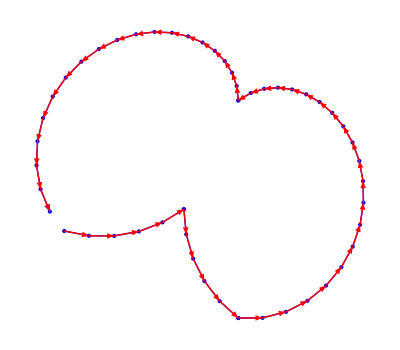

53

{{{-0.44,-0.08},1},{{-0.349088,-0.0975845},1},{{-0.256493,-0.0981036},1},{{-0.16539,-0.0815394},1},{{-0.0789036,-0.04846},1},{{0.,0.},2},{{0.00857415,-0.0921989},1},{{0.0340025,-0.181236},1},{{0.075413,-0.264057},1},{{0.131385,-0.337821},1},{{0.2,-0.4},2},{{0.28887,-0.399406},1},{{0.374986,-0.377296},1},{{0.454077,-0.336618},1},{{0.522824,-0.280662},1},{{0.578844,-0.212983},1},{{0.620671,-0.137255},1},{{0.647696,-0.0571013},1},{{0.660087,0.0240654},1},{{0.658656,0.103185},1},{{0.644714,0.177643},1},{{0.619913,0.245323},1},{{0.586096,0.304608},1},{{0.54517,0.354346},1},{{0.499005,0.393783},1},{{0.449365,0.422485},1},{{0.397872,0.440243},1},{{0.345984,0.446981},1},{{0.294993,0.442658},1},{{0.24602,0.427136},1},{{0.2,0.4},1},{{0.2,0.4},1},{{0.194097,0.453097},1},{{0.17713,0.501589},1},{{0.149994,0.544976},1},{{0.113471,0.582443},1},{{0.0683692,0.612983},1},{{0.0156239,0.635474},1},{{-0.0436255,0.648743},1},{{-0.107972,0.651642},1},{{-0.17569,0.643124},1},{{-0.244714,0.622357},1},{{-0.312646,0.588836},1},{{-0.3768,0.542509},1},{{-0.434299,0.483896},1},{{-0.482206,0.414184},1},{{-0.517693,0.335286},1},{{-0.538224,0.249861},1},{{-0.541741,0.16129},1},{{-0.526828,0.0736109},1},{{-0.492847,-0.0085481},1}}

```mathematica
pts={{-0.44000000000000006,-0.0799999999999999},{-0.34908833119391414,-0.09758450110568812},{-0.25649310027351224,-0.09810355316559355},{-0.16539000742970364,-0.08153935446671928},{-0.0789035776132942,-0.04846000045466636},{0.,0.},{0.,0.},{0.008574146204243405,-0.09219886236343526},{0.03400252088444672,-0.1812356186237945},{0.07541301763163244,-0.26405661211816595},{0.13138539783179792,-0.3378213656185442},{0.2,-0.4},{0.2,-0.4},{0.2888695748392632,-0.3994062738664452},{0.3749858035159918,-0.37729618092310946},{0.4540765530806895,-0.33661847770095066},{0.5228235840393997,-0.2806624980908578},{0.57884437810175,-0.2129830802154477},{0.6206706797124567,-0.13725453066628235},{0.6476964386965125,-0.05710130022657672},{0.6600874789729746,0.024065432600272718},{0.6586564939409265,0.10318475460388726},{0.644714376201137,0.17764281189943154},{0.6199131075399987,0.2453226644509633},{0.5860962024582475,0.30460772545547243},{0.5451700737645953,0.3543456305067364},{0.4990045725849914,0.39378336097709193},{0.44936493373343345,0.42248522204783506},{0.3978720587400722,0.44024284518472384},{0.3459844650319744,0.44698128097704964},{0.29499324025851703,0.4426575981269028},{0.246019635964924,0.4271362096467363},{0.20000000000000007,0.4},{0.2,0.4},{0.19409718613843474,0.453097434559981},{0.17713013434641206,0.5015891510829553},{0.14999434576245502,0.5449763406118092},{0.11347104090373572,0.5824433541028919},{0.06836921739820817,0.6129830802154478},{0.015623945230678726,0.6354736746542482},{-0.04362553985336798,0.6487434373157182},{-0.1079715411105705,0.6516415972398815},{-0.17568973296322848,0.6431240847025772},{-0.2447143762011368,0.6223571881005686},{-0.31264609268144605,0.5888360479150734},{-0.37680014130356654,0.5425092427385434},{-0.4342989033991689,0.483896370821264},{-0.48220603236049986,0.41418382537019627},{-0.5176930910334081,0.3352856543521314},{-0.5382241488963261,0.24986136837700526},{-0.5417407140091743,0.16129015584398132},{-0.5268284268480827,0.07361093425892784},{-0.49284676399671395,-0.008548104448456662}};
(*pts = Reverse[pts];*)
Graphics[{Blue, Arrow[pts],Point[pts],Red,Table[Arrow[{pts[[i]],pts[[i+1]]}],{i,1,Length[pts]-1}]}]
Length[pts]
Tally[pts]
```

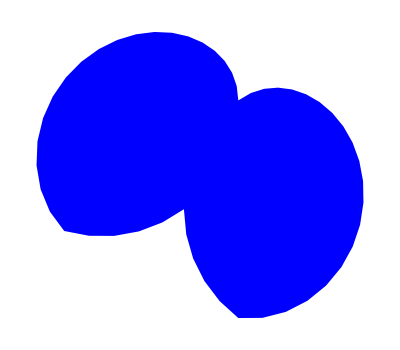

```mathematica
Graphics[{Blue, regi}]
```

```mathematica
Join[DeleteDuplicates[pts],{pts[[1]]}]
```

{{-0.44,-0.08},{-0.349088,-0.0975845},{-0.256493,-0.0981036},{-0.16539,-0.0815394},{-0.0789036,-0.04846},{0.,0.},{0.00857415,-0.0921989},{0.0340025,-0.181236},{0.075413,-0.264057},{0.131385,-0.337821},{0.2,-0.4},{0.28887,-0.399406},{0.374986,-0.377296},{0.454077,-0.336618},{0.522824,-0.280662},{0.578844,-0.212983},{0.620671,-0.137255},{0.647696,-0.0571013},{0.660087,0.0240654},{0.658656,0.103185},{0.644714,0.177643},{0.619913,0.245323},{0.586096,0.304608},{0.54517,0.354346},{0.499005,0.393783},{0.449365,0.422485},{0.397872,0.440243},{0.345984,0.446981},{0.294993,0.442658},{0.24602,0.427136},{0.2,0.4},{0.2,0.4},{0.194097,0.453097},{0.17713,0.501589},{0.149994,0.544976},{0.113471,0.582443},{0.0683692,0.612983},{0.0156239,0.635474},{-0.0436255,0.648743},{-0.107972,0.651642},{-0.17569,0.643124},{-0.244714,0.622357},{-0.312646,0.588836},{-0.3768,0.542509},{-0.434299,0.483896},{-0.482206,0.414184},{-0.517693,0.335286},{-0.538224,0.249861},{-0.541741,0.16129},{-0.526828,0.0736109},{-0.492847,-0.0085481},{-0.44,-0.08}}

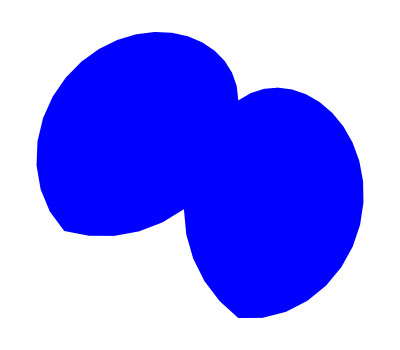

False

(√(5863757/10))/1000

{-4343/10000,4839/10000}

```mathematica
(*regi=Polygon[Join[DeleteDuplicates[Chop[pts]],{pts[[1]]}]];*)
(*regi=Polygon[Reverse[DeleteDuplicates[Chop[pts]]]];*)
ptsC = DeleteDuplicates[Round[pts,1/100000]];
regi=Polygon[ptsC];
Graphics[{Blue, regi}]
RegionMember[regi, {-1,1}]
RegionDistance[regi, {-1,1}]
p1= RegionNearest[regi, {-1,1}]
```

```mathematica
{0.20000000000000007,0.4}-{0.2,0.4}
```

{5.55112×10^-17,0.}

```mathematica
p1= RegionNearest[regi, {-1,1}];

Graphics[{Blue, regi, Green, Disk[Flatten@p1, 0.0125]}]
```

-Graphics-